```mathematica
dir="D:\\workingBuffer 2";
```

```mathematica
dir="D:\\newOutput";
```

```mathematica
indexOfEgg=6;
```

```mathematica
GetNumberOfOrganisms[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nFertile},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
nOrganisms="o"/.items//CountDistinct;
nFertile=Cases[{"o","ct"}/.items,{x_,indexOfEgg}->x]//CountDistinct;
{nOrganisms,nFertile}
]
```

```mathematica
GetNumberOfOrganisms[1522600]
```

{258,254}

```mathematica
head={"a","b","c"};itms={{1,2,3},{4,5,6}};
applyHeading[item_]:=MapThread[#1-> #2&,{head,item}];
applyHeading[itms//First]
```

{a→1,b→2,c→3}

```mathematica
f0=10;
fMax=1938800;
df=20000;
GetNumberOfOrganisms[fMax]//Print;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames]//Transpose;
```

{657,640}

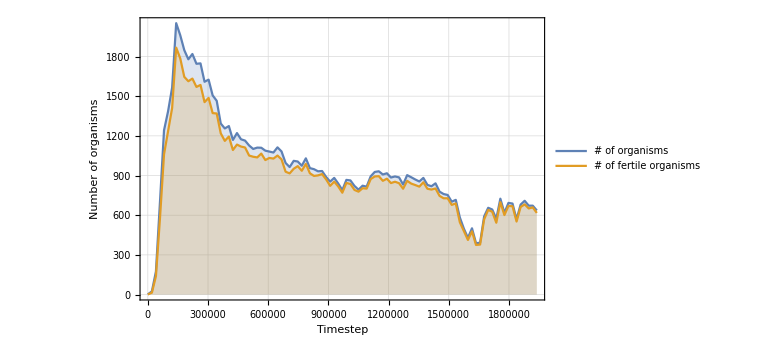

```mathematica
plot=ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
PlotLegends->Placed[{"# of organisms","# of fertile organisms"},Above],
ImageSize->Large,
GridLines->Automatic
]
```